```mathematica
<<KerrGeodesics`
```

```mathematica
KerrGeoSeparatrix[0.9,0.7,1]
```

3.07821

```mathematica
orbit=KerrGeoOrbit[0.9,20.5,0.7,1,Parametrization->"Darwin"];
{t,r,θ,ϕ}=orbit["Trajectory"];
```

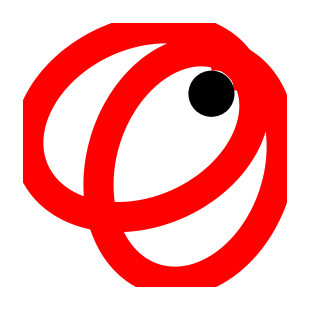

```mathematica
favicon=Show[
ParametricPlot[{r[χ] Cos[ϕ[χ]],r[χ]Sin[ϕ[χ]]},{χ,0,4π},AspectRatio->1,Axes->False,PlotStyle->{Thickness[0.07],Red},Background->None,ImageSize->310],
Graphics[{Black,Disk[{-1,-1},8]}]
]
```

```mathematica
SetDirectory["~/Desktop"]
Export["bhptoolkit_favicon.png",favicon,Background->None]
```

/Users/niels/Desktop

bhptoolkit_favicon.png

Then generate the favicons at http://www.favicomatic.com